```mathematica
(*交互式操作*)
Manipulate[Plot[function[frequency*x],{x,0,2 π}], {function, {Sin, Cos, Tan, Csc, Sec, Cot}},{frequency, 1, 5}]
```

```mathematica
(*展开*)
Expand[(x+1)^4]
```

1+4 x+6 x^2+4 x^3+x^4

```mathematica
Manipulate[Expand[(a+b)^n],{n,2,10,1}]
```

```mathematica
(*化简*)
Simplify[a^2+2*a*b+b^2]
```

(a+b)^2

```mathematica
(*因式分解*)
```

```mathematica
Factor[a^3+3 a^2 b+3a b^2+b^3]
```

(a+b)^3

```mathematica
(*定义函数*)
```

```mathematica
f[x_] = x * Sin[x] + x^2
```

x^2+x Sin[x]

```mathematica
f[3]
```

9+3 Sin[3]

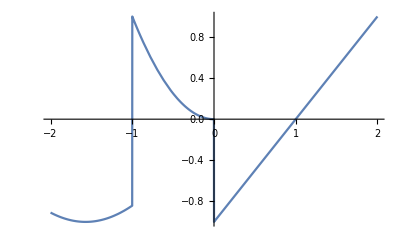

```mathematica
(*分段函数*)
f[x_]:=x-1/;x⩾0
f[x_]:=x^2/;(x>-1)&&(x<0)
f[x_]:= Sin[x]/;x⩽-1
Plot[f[x],{x,-2,2}]
```

```mathematica
(*多项式的代数运算*)
p1=a^2+3 a + 2; p2 = a + 1;
p1 + p2
```

3+4 a+a^2

```mathematica
Cancel[p1/p2]
```

2+a

```mathematica
(*方程*)
Roots[x^2-3 x + 2 == 0, x]
```

x==1||x==2

```mathematica
Solve[x^2 -3 x + 2 == 0]
```

{{x→1},{x→2}}

```mathematica
Solve[a x^2+ b x + c == 0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[{2 x + y == 0, x + 3 y - 3 == 0}, {x, y}]
```

{{x→-3/5,y→6/5}}

```mathematica
(*求和*)
Sum[i, {i, 1, 100}]
```

5050

```mathematica
NSum[1/(j!),{j, 1, Infinity}]
```

1.71828

```mathematica
(*求积*)
Product[i, {i, 1, 5}]
```

120

```mathematica
(*绘图*)
```

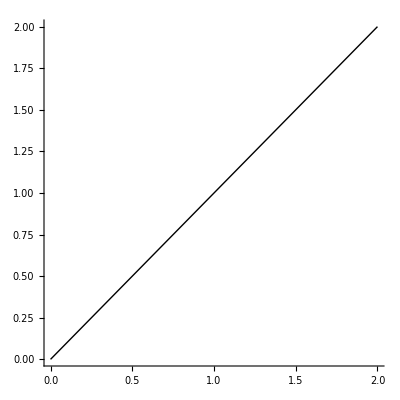

```mathematica
Show[Graphics[Line[{{0,0},{2,2}}]], Axes->True]
```

```mathematica
(*微积分*)
```

```mathematica
Limit[(√(x^2+2))/(3 x - 6),x->Infinity]
```

1/3

```mathematica
Limit[Sin[x]^2/x^2,x->0]
```

1

```mathematica
D[Exp[x] Sin[x],x]
```

ⅇ^x Cos[x]+ⅇ^x Sin[x]

```mathematica
(*绘制箭头*)
Graphics3D[Arrow[{{0,0,0},{1,1,1}}],Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-